```mathematica
∫_0^1 Cos[ ((4π/(Sqrt[3]*h))* Sin[θ])*t + ( (4π/Sqrt[3])*y)]ⅆy
```

(√3 Cos[(2 π (h+2 t Sin[θ]))/(√3 h)] Sin[(2 π)/(√3)])/(2 π)

```mathematica
f1 = Cos[ ((4π/(Sqrt[3]*h))* Sin[θ])*t + ( (4π/Sqrt[3])*y)]
Integrate[f1,{x,0,1}, {y,0,1}]
```

Cos[(4 π y)/(√3)+(4 π t Sin[θ])/(√3 h)]

(√3 Cos[(2 π (h+2 t Sin[θ]))/(√3 h)] Sin[(2 π)/(√3)])/(2 π)

```mathematica
f2 = Cos[ ((2π/h)* (Cos[θ]- (1/Sqrt[3])*Sin[θ]))*t + (2π * (x - (1/Sqrt[3])*y))]
Integrate[f2,{x, 0, 1},{y,0,1} ]
```

Cos[2 π (x-y/(√3))+(2 π t (Cos[θ]-Sin[θ]/(√3)))/h]

0

```mathematica
f3 = Cos[ ((2π/h)* (Cos[θ]+ (1/Sqrt[3])*Sin[θ]))*t + (2π * (x + (1/Sqrt[3])*y))]
Integrate[f3,{x, 0, 1},{y,0,1} ]
```

Cos[2 π (x+y/(√3))+(2 π t (Cos[θ]+Sin[θ]/(√3)))/h]

0

```mathematica
ffull = f1+f2+f3
Integrate[ffull,{x, 0, 1},{y,0,√3} ]
```

Cos[(4 π y)/(√3)+(4 π t Sin[θ])/(√3 h)]+Cos[2 π (x-y/(√3))+(2 π t (Cos[θ]-Sin[θ]/(√3)))/h]+Cos[2 π (x+y/(√3))+(2 π t (Cos[θ]+Sin[θ]/(√3)))/h]

0

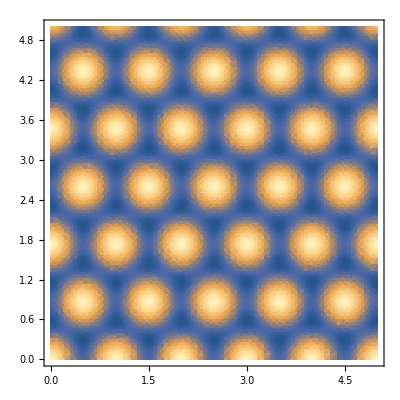

```mathematica
ffull1=(Cos[(4 π y)/(√3)+(4 π t Sin[θ])/(√3 h)]+Cos[2 π (x-y/(√3))+(2 π t (Cos[θ]-Sin[θ]/(√3)))/h]+Cos[2 π (x+y/(√3))+(2 π t (Cos[θ]+Sin[θ]/(√3)))/h])/.{θ->0,t->0,h->20};
DensityPlot[f,{x, 0, 5},{y,0,5},PlotPoints->50]
```

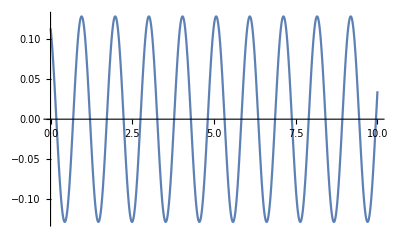

```mathematica
Plot[(√3 Cos[(2 π (h+2 t Sin[θ]))/(√3 h)] Sin[(2 π)/(√3)])/(2 π)/.{θ->1,h->1},{t,0,10}]
```

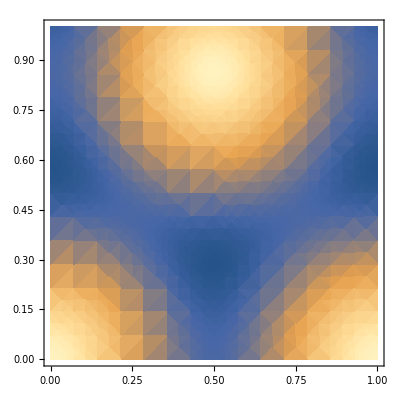
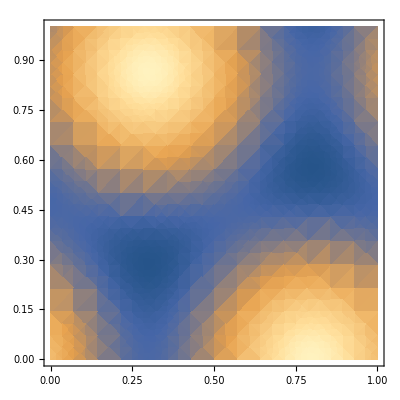
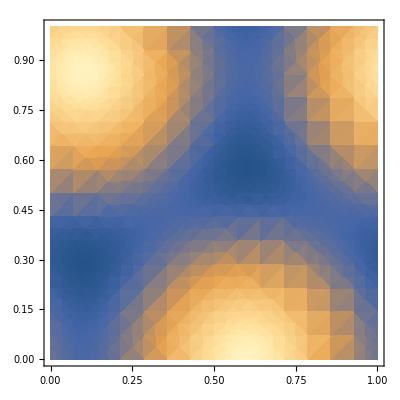
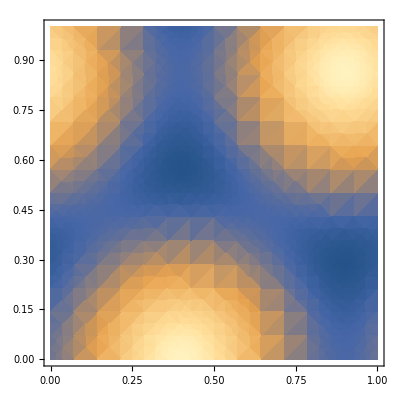
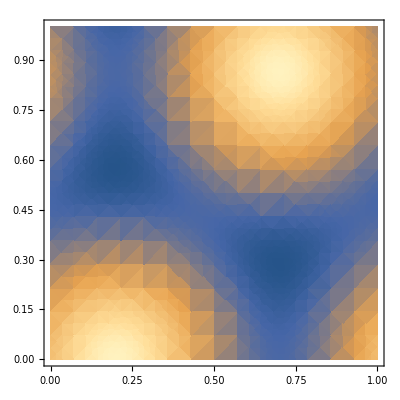
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffull2[ϕ1_,ϕ2_,h_]:=(Cos[(4 π ϕ2)/(√3)+(4 π y)/(√3 h)]+Cos[2 π (ϕ1-ϕ2/(√3))+(2 π (x-y/(√3)))/h]+Cos[2 π (ϕ1+ϕ2/(√3))+(2 π (x+y/(√3)))/h]);
Table[DensityPlot[ffull2[ϕ,0,1],{x, 0, 1},{y,0,1}],{ϕ,0,1,.2}]
```

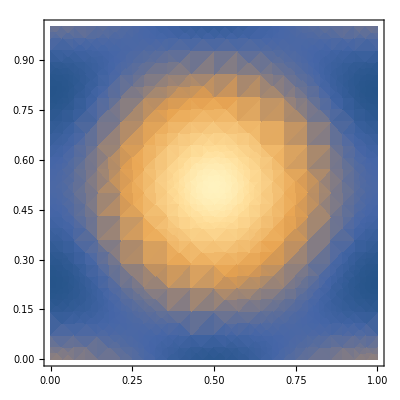
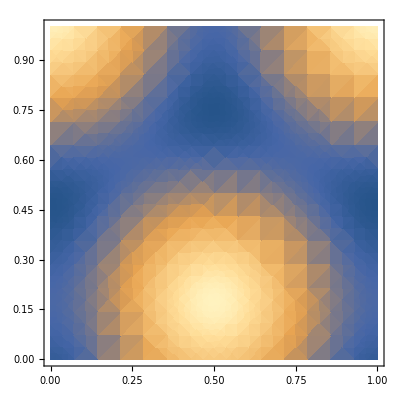
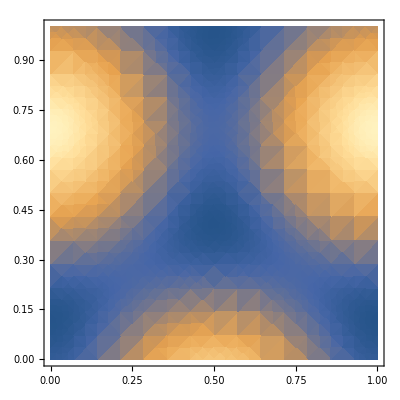
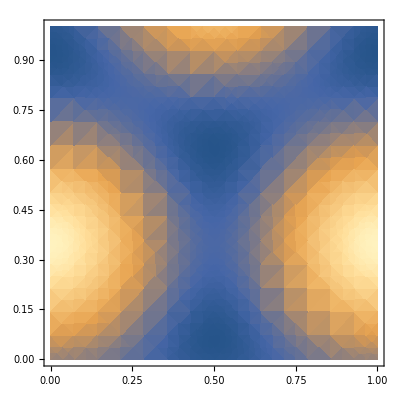
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ffull3[ϕ1_,ϕ2_,h_]:=(Cos[(4 π ϕ2)/(√3)+(4 π y)/(√3 h)]+Cos[2 π (ϕ1-ϕ2/(√3))+(2 π (x-y/(√3)))/h]+Cos[2 π (ϕ1+ϕ2/(√3))+(2 π (x+y/(√3)))/h]);
Table[DensityPlot[ffull3[0,ϕ,1],{x, 0, 1},{y,0,1}],{ϕ,0,√3,√3/5}]
```

```mathematica
f10=(Cos[(4 π y)/(√3)+(4 π t Sin[θ])/(√3 h)]+Cos[2 π (x-y/(√3))+(2 π t (Cos[θ]-Sin[θ]/(√3)))/h]+Cos[2 π (x+y/(√3))+(2 π t (Cos[θ]+Sin[θ]/(√3)))/h]);
Integrate[f10,{x, 0, 1},{y,0,√3}]
```

0